```mathematica
Clear[IFS, funcionafin, AffineMap, x,y,T]; (*Borra por si acaso*)
funcionafin[scaleX_,scaleY_,rotateX_, rotateY_,translateX_,translateY_][{x_,y_}]:= {Cos[rotateX],Sin[rotateX]}*scaleX*x+{-Sin[rotateY],Cos[rotateY]}*scaleY*y+{translateX,translateY}
```

```mathematica
AffineMap[scaleX_,scaleY_,rotateX_, rotateY_,translateX_,translateY_][T_List]:= Map[funcionafin[scaleX,scaleY,rotateX,rotateY,translateX,translateY][#]&,T];
IFS[AF_][T_]:= Flatten[Outer[#1[#2] &,AF,T,1,1],1];
```

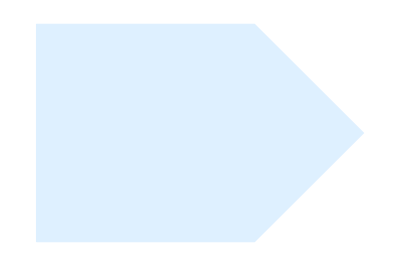

```mathematica
pol = {{{0,0},{1,0},{1.5,0.5},{1,1},{0,1},{0,0}}};
motivo = Polygon[pol];
Gmotivo = Graphics[{EdgeForm[Thin],LightBlue, motivo}]
```

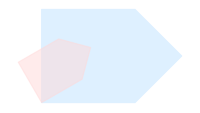

```mathematica
rotesc = IFS[{AffineMap[.5,.5,Pi/6,Pi/6,0,0]}];

A1 = Graphics[{EdgeForm[Thin],Opacity[0.5,LightRed],Polygon[Nest[rotesc,pol,1]]}];
Show[Gmotivo, A1, ImageSize->200]
```

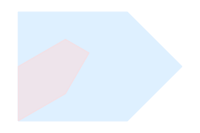

```mathematica
rotX =IFS[{AffineMap[0.5,0.5,Pi/6,0.0,0.0,0.0]}];
A2 = Graphics[{EdgeForm[Thin],Opacity[0.5,LightRed],Polygon[Nest[rotX,pol,1]]}];
Show[Gmotivo, A2, ImageSize->200]
```

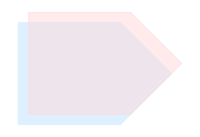

```mathematica
rotX =IFS[{AffineMap[1,1,0,0,0.1,0.1]}];
A1 = Graphics[{EdgeForm[Thin],Opacity[0.5,LightRed],Polygon[Nest[rotX,pol,1]]}];
Show[Gmotivo, A1, ImageSize->200]
```

```mathematica
rotX =IFS[{AffineMap[1,1,Pi,0,0.0,0.0]}];
A1 = Graphics[{EdgeForm[Thin],Opacity[0.5,LightRed],Polygon[Nest[rotX,pol,1]]}];
Show[Gmotivo, A1, ImageSize->200]
```

```mathematica
w1=IFS[{AffineMap[0.5,0.5,0,0,0,0]}];
w2=IFS[{AffineMap[0.5,0.5,0,0,1/2,0]}];
w3=IFS[{AffineMap[0.5,0.5,0,0,1/4,Sqrt[3]/4]}];
tri = {{{0,0},{1,0},{1/2,Sqrt[3]/2}}};
```

```mathematica
AF = {AffineMap[0.5,0.5,0,0,0,0],AffineMap[0.5,0.5,0,0,1/2,0], AffineMap[0.5,0.5,0,0,1/4,Sqrt[3]/4]};
ifs1 = IFS[AF];
gifs1[x_,n_]:=Graphics[Polygon[Nest[ifs1,x,n]],Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{0,1},{0,1}},Ticks->{{0,1},{0,1}}];
gifs1[tri,1]
```

Outer::ipnfm: Positive machine-sized integer or Infinity expected at position 3 in Outer[#1[#2]&,{AffineMap[0.5,0.5,0,0,0,0],AffineMap[0.5,0.5,0,0,1/2,0],AffineMap[0.5,0.5,0,0,1/4,(√3)/4]},tri,1,1].

-Graphics-

```mathematica
Show[GraphicsGrid[{Table[gifs1[tri,n],{n,0,1}]}],ImageSize->400]
```

```mathematica
gifs1[tri,8]
```

```mathematica
cosa = {{{0,0},{1,0},{1,1},{0,1}}};
gifs1[cosa,8]
```

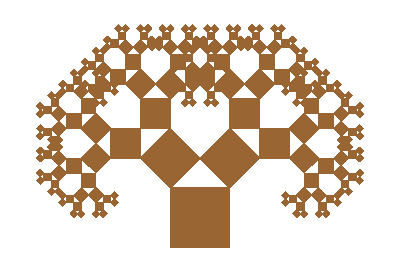

```mathematica
cosa = {{{0,0},{1,0},{1,1},{0,1}}};
AF = {AffineMap[1,1,0,0,0,0],AffineMap[1/Sqrt[2],1/Sqrt[2],Pi/4, Pi/4,0,1],  AffineMap[1/Sqrt[2],1/Sqrt[2],-Pi/4,-Pi/4,1/2,1+1/2]};
ifs1 = IFS[AF];
gifs1[x_,n_]:=Graphics[{Brown, Polygon[Nest[ifs1,x,n]]},Axes->False,AxesOrigin->{0,0},AspectRatio->Automatic,Ticks->{{0,1},{0,1}}];
gifs1[cosa,7]
```

```mathematica
cosa = {{{0,0},{1,0},{1,1},{0,1}}};
AF = {AffineMap[1,1,0,0,0,0],AffineMap[1/Sqrt[2],1/Sqrt[2],Pi/4, Pi/4,0,1],  AffineMap[1/Sqrt[2],1/Sqrt[2],-Pi/4,-Pi/4,1/2,1+1/2]};
ifs1 = IFS[AF];
gifs1[x_,n_]:=Graphics[Polygon[Nest[ifs1,x,n]],Axes->False,AxesOrigin->{0,0},AspectRatio->Automatic,Ticks->{{0,1},{0,1}}];
gifs1[cosa,7]
```

```mathematica
fern = IFS[{AffineMap[0.85,0.85,-2.5*Pi/180,-2.5*Pi/180,0,1.6],AffineMap[0.3,0.34,49*Pi/180,49*Pi/180,0,1.6], AffineMap[0.3,0.34,120*Pi/180,-50*Pi/180,0,.44],AffineMap[0,0.3,0,0,0,0]}];
cua = {{{0,0},{1,0},{1,2},{0,2}}};
gfern[x_,n_]:= Graphics[{Brown,Line[Nest[fern,x,n]]}, Axes->False,AspectRatio->Automatic];
gfern[cua,8]
```

-Graphics-

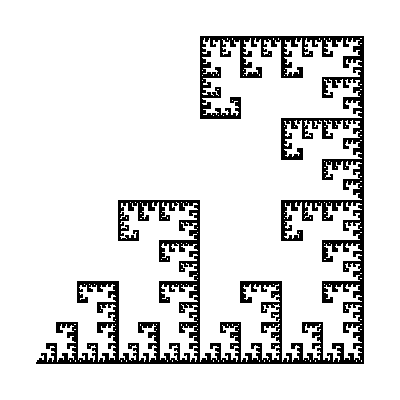

```mathematica
cosa = {{{0,0},{1,0},{1,1},{0,1}}};
AF = {AffineMap[0.5,0.5,0,0,0,0],AffineMap[0.5,0.5,0, 0,0.5,0],  AffineMap[0.5,0.5,Pi/2,Pi/2,1,1/2]};
ifs1 = IFS[AF];
gifs1[x_,n_]:=Graphics[Polygon[Nest[ifs1,x,n]],Axes->False,AxesOrigin->{0,0},AspectRatio->Automatic,Ticks->{{0,1},{0,1}}];
gifs1[cosa,8]
```